## Reconsideration of ICPC Chapter 2

### Separate the “function” in construction of the Hamiltonian and make it more of a pure function (2.2.1)

#### Existing code

The existing strategy uses global variables to define the constants and embeds the function defining the Hamiltonian matrix into the Table function:

```mathematica
hbar=1;(*define variables in atomic units*)
nPoints=100;(*how many points on the finite grid*)
L=5;(*length of the box in Bohr radii*)
m=1;(*set m=1 me*)
a=L/(nPoints+1); (*spacing between points*)
t=hbar^2/(2*m*a^2);(*constant for finite difference*)
```

```mathematica
V[x_]:=0;(*define the potential as zero everywhere for 1D PIB*)
```

```mathematica
(*set up the Hamiltonian matrix*)
hMatr=Table[N[
(V[i*a]+2*t)*KroneckerDelta[i,j]-t*KroneckerDelta[i,j-1]-t*KroneckerDelta[i,j+1]]
,{i,1,nPoints},{j,1,nPoints}];
```

#### Reconsideration: Define a pure function for each element in the Hamiltonian

Begin by defining a function that calculates each individual Hamiltonian matrix element.  It takes a potential function and length as input, along with the other parameters:

```mathematica
V[x_]:=0;(*define the potential as zero everywhere for 1D PIB*)

(*define a function for a single matrix entry, addressed by i & j*)

hamiltonianMatrixElement[i_Integer,j_Integer,V_,L_?NumericQ,
nPoints_Integer:100,m_:1,hbar_:1]:=With[
{a=L/(nPoints+1)},
With[{t=hbar^2/(2*m*a^2)},
(V[i*a]+2*t)*KroneckerDelta[i,j]-t*KroneckerDelta[i,j-1]-t*KroneckerDelta[i,j+1]]//N]

hMatr=Table[
hamiltonianMatrixElement[i,j,V,5],
{i,100},{j,100}];
```

.Notice that V is defined as a function, and then we pass the function-V as an argument to hamiltonianMatrixElement[].  Yes, that is right...the arguments to functions can be other functions. (This is what is known as supporting first class functions, and is a common strategy in functional programming languages.)

### Use fewer list-index operations and more vector operations (2.2.3)

In the interest of making the code more like typical procedural-first language (Fortran77, Python) idioms, many of the operations that involve constructing a list form other lists rely on index arithmetic.  In Mathematica (as in MATLAB), it is always faster to do this as vector operations on the list.  For example:

```mathematica
(*set up the problem*)
L=5;
energy1DPIB[n_,L_,m_:1,hbar_:1]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
finiteDiffResults=Reverse[Eigenvalues[hMatr,-100]];exactResults=Table[N[energy1DPIB[n,L]],{n,1,100}];
```

#### Original approach

```mathematica
percentError=Table[(finiteDiffResults[[n]]-exactResults[[n]])/exactResults[[n]]*100,{n,1,100}];
```

#### New approach

Instead, let us take advantage of the fact that these are vectors.  The common arithmetic operators (+, -, *, /) operate elementwise, allowing us to replace the Table above with a simple arithmetic expression:

```mathematica
percentError=(finiteDiffResults-exactResults)/exactResults*100;
```

As a side note, since writing the book, a new function ListLinePlot has been introduced, which allows us to avoid having to write Joined all the time.  Mesh turns on/off displaying the points (otherwise it’s just a line); this can also be accomplished using PlotMarkers->Automatic

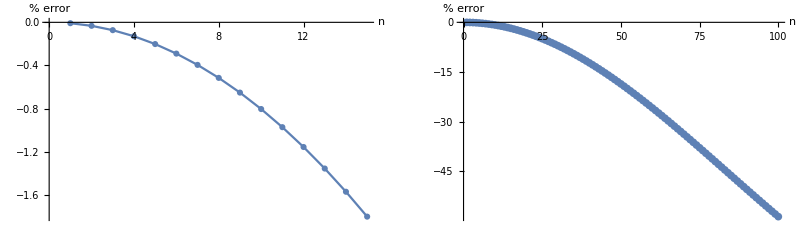

```mathematica
GraphicsRow[
{ListLinePlot[percentError[[1;;15]],
AxesLabel->{"n","% error"},PlotMarkers->Automatic],
ListLinePlot[percentError,
AxesLabel->{"n","% error"},Mesh->All]}]
```

As an advanced tip, I would probably write this as a Map (/@) over the inputs, and apply the GraphicsRow function as a postfix.  This emphasizes the plot construction

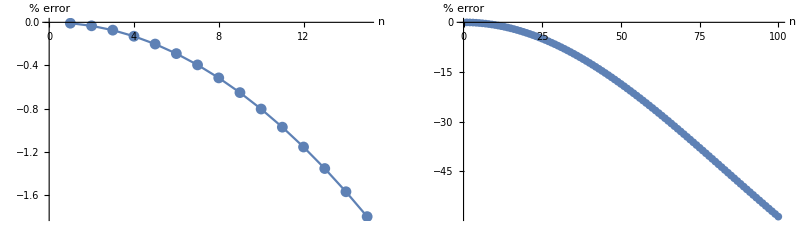

```mathematica
ListLinePlot[#,AxesLabel->{"n","% error"},Mesh->All]&/@
{percentError[[1;;15]],percentError}//GraphicsRow
```

### More vector-based operations (2.2.4)

We can vectorize sums instead of introducing an explicit loop.  This can be singificantly faster, as well as simplifying the code.

#### Original code:

```mathematica
(*demonstration of normalization*)
estate2=Reverse[Eigenvectors[hMatr,-2]][[2]]/Sqrt[a];Sum[estate2[[j]]^2*a,{j,1,nPoints}]
```

1.

#### Reconsiderations:

We don’t  have to reverse the list of eigenvectors, but instead can address it “from the back” with a negative index

We don't need to Sum over an explicit index, but instead could compute the Total of the elements in the vector (regardless of its length); the exponential operator applies elementwise.

```mathematica
estate2=Eigenvectors[hMatr,-2][[-2]]/Sqrt[a];
Total[estate2^2]*a
```

1.

Of course, we can always  use a dot-product (as demonstrated in the text), which is still likely to be the fastest, although the difference is negligible:

```mathematica
RepeatedTiming[ Total[estate2^2]*a] (*Total is slightly slower*)
```

{3.01116×10^-6,1.}

```mathematica
RepeatedTiming[ (estate2.estate2)*a]  (*dot products slightly faster*)
```

{4.32929×10^-7,1.}

### Rescaling points on a ListPlot graphic (2.2.4)

In the book, we use a Table to create a list of {x_j, ψ(x_j)} pairs, but there are other ways to do this.

#### Original

```mathematica
(*plotting grid of points*)
estate2withcoords=Table[{N[a*j],estate2[[j]]},{j,1,nPoints}];ListPlot[estate2withcoords,AxesLabel-> {"x","ψ"}]
```

#### Reconsideration 1

Make the list of pairs, as before, but do it in a more functional way

In the above example we don't include j = 0, so we get rid of it by only taking the Rest of the Subdivide list result.

Using With just lets us see this more clearly, but we would be free to put this inside Transpose

The subdivision chosen in the book makes this a little more annoying as the grid points are actually inside the boundaries by one point:

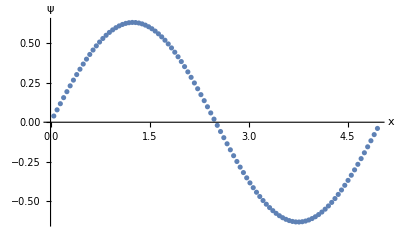

```mathematica
estate2withcoords=With[
{x=Subdivide[L,101][[2;;-2]]} (*drop first and last points*),
Transpose[{x,estate2}]];

ListPlot[estate2withcoords,AxesLabel-> {"x","ψ"}]
```

#### Reconsideration 2

In this problem, we do not actually need the values of x for any other purpose than plotting, so alternatively we could just change the range over which data is plotted, using the DataRange option for the plot functions:

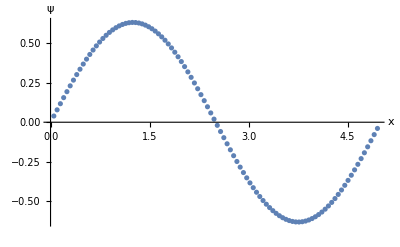

```mathematica
ListPlot[estate2,AxesLabel-> {"x","ψ"},DataRange->{5/100,5-5/100}]
```

### More vector operations instead of explicit iterations (2.2.5)

Yet another replacement of an explicit sum with an implicit vectorization processes.

#### Original

```mathematica
xcoords=Table[ N[a*i], {i,1,nPoints}]
Sum[(Conjugate[estate2[[i]]]*xcoords[[i]]*estate2[[i]])*a, {i,1,nPoints}]
```

{0.049505,0.0990099,0.148515,0.19802,0.247525,0.29703,0.346535,0.39604,0.445545,0.49505,0.544554,0.594059,0.643564,0.693069,0.742574,0.792079,0.841584,0.891089,0.940594,0.990099,1.0396,1.08911,1.13861,1.18812,1.23762,1.28713,1.33663,1.38614,1.43564,1.48515,1.53465,1.58416,1.63366,1.68317,1.73267,1.78218,1.83168,1.88119,1.93069,1.9802,2.0297,2.07921,2.12871,2.17822,2.22772,2.27723,2.32673,2.37624,2.42574,2.47525,2.52475,2.57426,2.62376,2.67327,2.72277,2.77228,2.82178,2.87129,2.92079,2.9703,3.0198,3.06931,3.11881,3.16832,3.21782,3.26733,3.31683,3.36634,3.41584,3.46535,3.51485,3.56436,3.61386,3.66337,3.71287,3.76238,3.81188,3.86139,3.91089,3.9604,4.0099,4.05941,4.10891,4.15842,4.20792,4.25743,4.30693,4.35644,4.40594,4.45545,4.50495,4.55446,4.60396,4.65347,4.70297,4.75248,4.80198,4.85149,4.90099,4.9505}

2.5

#### Reconsideration

```mathematica
xcoords=N@Subdivide[L,101][[2;;-2]];
Total[Conjugate[estate2]*xcoords*estate2]*a
```

2.5

(Again, the text demonstrates how to do this with a dot-product, which is still the best way, as noted above.)

Last edited: 31 January 2023